```mathematica
Quit
```

### Carga de paqueterias xAct

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

### Variación de la traza

#### Obtener las ecuaciones de Escalaron

```mathematica
DefManifold[M4,4,{a,b,c,d,e,f,i,j,k,l,m,n}];
DefMetric[-1,metric[-a,-b],CD,SymbolOfCovD->{"|","∇"},PrintAs->"g"];
DefMetricPerturbation[metric,h,ϵ];
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

** DefTensor: Defining symmetric metric tensor metric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrametric[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrametric†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-a,-b].

** DefTensor: Defining weight +2 density Detmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametermetric.

** DefTensor: Defining tensor Perturbationmetric[LI[order],-a,-b].

** DefParameter: Defining parameter ϵ.

** DefTensor: Defining tensor h[LI[order],-a,-b].

```mathematica
DefScalarFunction[f1];
DefScalarFunction[f2];
DefConstantSymbol[Rbar];
DefConstantSymbol[κ];
DefTensor[rho[],M4,PrintAs->"ρ"];
lm[]:=-rho[]; (*Tal cual, Lm=-rho*)
DefTensorPerturbation[deltarho[LI[order]],rho[],M4]; (*Perturbacion de la rho, por definicion*)
```

** DefScalarFunction: Defining scalar function f1.

** DefScalarFunction: Defining scalar function f2.

** DefConstantSymbol: Defining constant symbol Rbar.

** DefConstantSymbol: Defining constant symbol κ.

** DefTensor: Defining tensor rho[].

** DefTensor: Defining tensor deltarho[LI[order]].

```mathematica
Tdd[-mu_,-nu_]:=-rho[] metric[-mu,-nu];(*Pensando en TUd=(-rho, rho, rho, rho).*)
BoxCD[expr_]:=CD[a][CD[-a][expr]];
DeltaCD[-mu_,-nu_][expr_]:=CD[-mu][CD[-nu][expr]]-metric[-mu,-nu] BoxCD[expr];
```

```mathematica
Xf[]:=f1'[RicciScalarCD[]]+2 f2'[RicciScalarCD[]] lm[];

eqm[-mu_,-nu_]:=Xf[] RicciCD[-mu,-nu]-1/2 metric[-mu,-nu] f1[RicciScalarCD[]]-DeltaCD[-mu,-nu][Xf[]]-f2[RicciScalarCD[]] Tdd[-mu,-nu];
```

```mathematica
trEqm=metric[a,b] eqm[-a,-b]//ToCanonical//ContractMetric//ToCanonical (*Traza sin perturbar*)
```

-2 f1[R[∇]]+4 f2[R[∇]] ρ+R[∇] f1'[R[∇]]-2 ρ R[∇] f2'[R[∇]]-6 ∇_a ∇^a ρ f2'[R[∇]]+3 ∇_a ∇^a R[∇] f1''[R[∇]]-6 ρ ∇_a ∇^a R[∇] f2''[R[∇]]-12 ∇_a R[∇] ∇^a ρ f2''[R[∇]]+3 ∇_a R[∇] ∇^a R[∇] f1^(3)[R[∇]]-6 ρ ∇_a R[∇] ∇^a R[∇] f2^(3)[R[∇]]

```mathematica
EOM1trace=Perturbation[trEqm,1]; (*Perturbar la traza a primer orden*)
EOM1trace=EOM1trace//ExpandPerturbation//ContractMetric//ToCanonical//ContractMetric
```

4 deltarho | 1
  f2[R[∇]]+h | 1 | a | b
  |   |   R[∇] |   |  
a | b f1'[R[∇]]-∇_b ∇_a h | 1 | a | b
  |   |   f1'[R[∇]]+∇_b ∇^b h | 1 | a |  
  |   | a f1'[R[∇]]-2 h | 1 | a | b
  |   |   ρ R[∇] |   |  
a | b f2'[R[∇]]-2 deltarho | 1
  R[∇] f2'[R[∇]]-6 ∇_a ∇^a deltarho | 1
  f2'[R[∇]]-3 ∇_a h | 1 | b |  
  |   | b ∇^a ρ f2'[R[∇]]+6 ∇^a ρ ∇_b h | 1 |   | b
  | a |   f2'[R[∇]]+2 ρ ∇_b ∇_a h | 1 | a | b
  |   |   f2'[R[∇]]-2 ρ ∇_b ∇^b h | 1 | a |  
  |   | a f2'[R[∇]]+6 h | 1 |   |  
  | a | b ∇^b ∇^a ρ f2'[R[∇]]-h | 1 | a | b
  |   |   R[∇] |   |  
a | b R[∇] f1''[R[∇]]+3/2 ∇_a h | 1 | b |  
  |   | b ∇^a R[∇] f1''[R[∇]]-3 ∇^a R[∇] ∇_b h | 1 |   | b
  | a |   f1''[R[∇]]+R[∇] ∇_b ∇_a h | 1 | a | b
  |   |   f1''[R[∇]]-R[∇] ∇_b ∇^b h | 1 | a |  
  |   | a f1''[R[∇]]-3 h | 1 |   |  
  | a | b ∇^b ∇^a R[∇] f1''[R[∇]]-3 R[∇] | a | b
  |   ∇_c ∇^c h | 1 |   |  
  | a | b f1''[R[∇]]-3 h | 1 | a | b
  |   |   ∇_c ∇^c R[∇] |   |  
a | b f1''[R[∇]]+3 ∇_c ∇^c ∇_b ∇_a h | 1 | a | b
  |   |   f1''[R[∇]]-3 ∇_c ∇^c ∇_b ∇^b h | 1 | a |  
  |   | a f1''[R[∇]]-6 ∇_c R[∇] |   |  
a | b ∇^c h | 1 | a | b
  |   |   f1''[R[∇]]+2 h | 1 | a | b
  |   |   ρ R[∇] |   |  
a | b R[∇] f2''[R[∇]]+6 h | 1 | b | c
  |   |   R[∇] |   |  
b | c ∇_a ∇^a ρ f2''[R[∇]]-6 deltarho | 1
  ∇_a ∇^a R[∇] f2''[R[∇]]-12 ∇_a R[∇] ∇^a deltarho | 1
  f2''[R[∇]]+12 R[∇] | b | c
  |   ∇_a h | 1 |   |  
  | b | c ∇^a ρ f2''[R[∇]]+12 h | 1 | b | c
  |   |   ∇_a R[∇] |   |  
b | c ∇^a ρ f2''[R[∇]]-12 ∇_a ∇_c ∇_b h | 1 | b | c
  |   |   ∇^a ρ f2''[R[∇]]+12 ∇_a ∇_c ∇^c h | 1 | b |  
  |   | b ∇^a ρ f2''[R[∇]]-3 ρ ∇_a h | 1 | b |  
  |   | b ∇^a R[∇] f2''[R[∇]]+6 ρ ∇^a R[∇] ∇_b h | 1 |   | b
  | a |   f2''[R[∇]]-2 ρ R[∇] ∇_b ∇_a h | 1 | a | b
  |   |   f2''[R[∇]]+2 ρ R[∇] ∇_b ∇^b h | 1 | a |  
  |   | a f2''[R[∇]]+12 h | 1 |   |  
  | a | b ∇^a ρ ∇^b R[∇] f2''[R[∇]]+6 h | 1 |   |  
  | a | b ρ ∇^b ∇^a R[∇] f2''[R[∇]]-6 ∇_a ∇^a ρ ∇_c ∇_b h | 1 | b | c
  |   |   f2''[R[∇]]+6 ρ R[∇] | a | b
  |   ∇_c ∇^c h | 1 |   |  
  | a | b f2''[R[∇]]+6 ∇_a ∇^a ρ ∇_c ∇^c h | 1 | b |  
  |   | b f2''[R[∇]]+6 h | 1 | a | b
  |   |   ρ ∇_c ∇^c R[∇] |   |  
a | b f2''[R[∇]]-6 ρ ∇_c ∇^c ∇_b ∇_a h | 1 | a | b
  |   |   f2''[R[∇]]+6 ρ ∇_c ∇^c ∇_b ∇^b h | 1 | a |  
  |   | a f2''[R[∇]]+12 ρ ∇_c R[∇] |   |  
a | b ∇^c h | 1 | a | b
  |   |   f2''[R[∇]]-3 h | 1 | b | c
  |   |   R[∇] |   |  
b | c ∇_a ∇^a R[∇] f1^(3)[R[∇]]-6 R[∇] | b | c
  |   ∇_a h | 1 |   |  
  | b | c ∇^a R[∇] f1^(3)[R[∇]]-6 h | 1 | b | c
  |   |   ∇_a R[∇] |   |  
b | c ∇^a R[∇] f1^(3)[R[∇]]+6 ∇_a ∇_c ∇_b h | 1 | b | c
  |   |   ∇^a R[∇] f1^(3)[R[∇]]-6 ∇_a ∇_c ∇^c h | 1 | b |  
  |   | b ∇^a R[∇] f1^(3)[R[∇]]-3 h | 1 |   |  
  | a | b ∇^a R[∇] ∇^b R[∇] f1^(3)[R[∇]]+3 ∇_a ∇^a R[∇] ∇_c ∇_b h | 1 | b | c
  |   |   f1^(3)[R[∇]]-3 ∇_a ∇^a R[∇] ∇_c ∇^c h | 1 | b |  
  |   | b f1^(3)[R[∇]]+6 h | 1 | b | c
  |   |   ρ R[∇] |   |  
b | c ∇_a ∇^a R[∇] f2^(3)[R[∇]]+12 h | 1 | b | c
  |   |   R[∇] |   |  
b | c ∇_a R[∇] ∇^a ρ f2^(3)[R[∇]]+12 ρ R[∇] | b | c
  |   ∇_a h | 1 |   |  
  | b | c ∇^a R[∇] f2^(3)[R[∇]]+12 h | 1 | b | c
  |   |   ρ ∇_a R[∇] |   |  
b | c ∇^a R[∇] f2^(3)[R[∇]]-6 deltarho | 1
  ∇_a R[∇] ∇^a R[∇] f2^(3)[R[∇]]-12 ρ ∇_a ∇_c ∇_b h | 1 | b | c
  |   |   ∇^a R[∇] f2^(3)[R[∇]]+12 ρ ∇_a ∇_c ∇^c h | 1 | b |  
  |   | b ∇^a R[∇] f2^(3)[R[∇]]+6 h | 1 |   |  
  | a | b ρ ∇^a R[∇] ∇^b R[∇] f2^(3)[R[∇]]-6 ρ ∇_a ∇^a R[∇] ∇_c ∇_b h | 1 | b | c
  |   |   f2^(3)[R[∇]]-12 ∇_a R[∇] ∇^a ρ ∇_c ∇_b h | 1 | b | c
  |   |   f2^(3)[R[∇]]+6 ρ ∇_a ∇^a R[∇] ∇_c ∇^c h | 1 | b |  
  |   | b f2^(3)[R[∇]]+12 ∇_a R[∇] ∇^a ρ ∇_c ∇^c h | 1 | b |  
  |   | b f2^(3)[R[∇]]-3 h | 1 | b | c
  |   |   R[∇] |   |  
b | c ∇_a R[∇] ∇^a R[∇] f1^(4)[R[∇]]+3 ∇_a R[∇] ∇^a R[∇] ∇_c ∇_b h | 1 | b | c
  |   |   f1^(4)[R[∇]]-3 ∇_a R[∇] ∇^a R[∇] ∇_c ∇^c h | 1 | b |  
  |   | b f1^(4)[R[∇]]+6 h | 1 | b | c
  |   |   ρ R[∇] |   |  
b | c ∇_a R[∇] ∇^a R[∇] f2^(4)[R[∇]]-6 ρ ∇_a R[∇] ∇^a R[∇] ∇_c ∇_b h | 1 | b | c
  |   |   f2^(4)[R[∇]]+6 ρ ∇_a R[∇] ∇^a R[∇] ∇_c ∇^c h | 1 | b |  
  |   | b f2^(4)[R[∇]]

```mathematica
(*Condiciones de fondo*)
backgroundRules={RicciScalarCD[]->Rbar,RicciCD[a_,b_]:>Rbar/4 metric[a,b],RicciCD[-a_,-b_]:>Rbar/4 metric[-a,-b],CD[-a_][rho[]]->0,CD[a_][rho[]]->0}; (*En un fluido perfecto, la ec, de no continuidad se reduce a la de continuidad, rho->0*)

TrPertBG=EOM1trace/. {Perturbation[rho[]]->deltarho[xAct`xTensor`LI[1]],Perturbation[rho[],1]->deltarho[xAct`xTensor`LI[1]]}//.backgroundRules//ToCanonical//ContractMetric//ToCanonical//Simplify (*Traza perturbada con el Bg de DeSitter*)
```

-∇_b ∇_a h | 1 | a | b
  |   |   f1'[Rbar]+∇_b ∇^b h | 1 | a |  
  |   | a f1'[Rbar]-6 ∇_a ∇^a deltarho | 1
  f2'[Rbar]+2 ρ ∇_b ∇_a h | 1 | a | b
  |   |   f2'[Rbar]-2 ρ ∇_b ∇^b h | 1 | a |  
  |   | a f2'[Rbar]+deltarho | 1
  (4 f2[Rbar]-2 Rbar f2'[Rbar])+Rbar ∇_b ∇_a h | 1 | a | b
  |   |   f1''[Rbar]-7/4 Rbar ∇_b ∇^b h | 1 | a |  
  |   | a f1''[Rbar]+3 ∇_c ∇^c ∇_b ∇_a h | 1 | a | b
  |   |   f1''[Rbar]-3 ∇_c ∇^c ∇_b ∇^b h | 1 | a |  
  |   | a f1''[Rbar]-2 Rbar ρ ∇_b ∇_a h | 1 | a | b
  |   |   f2''[Rbar]+7/2 Rbar ρ ∇_b ∇^b h | 1 | a |  
  |   | a f2''[Rbar]-6 ρ ∇_c ∇^c ∇_b ∇_a h | 1 | a | b
  |   |   f2''[Rbar]+6 ρ ∇_c ∇^c ∇_b ∇^b h | 1 | a |  
  |   | a f2''[Rbar]+1/4 Rbar h | 1 | a |  
  |   | a (f1'[Rbar]-2 ρ f2'[Rbar]-Rbar f1''[Rbar]+2 Rbar ρ f2''[Rbar])

```mathematica
(*Aplicación del Gauge de Lorentz y las derivadas de f1*)
```

```mathematica
GaugeLorenz=MakeRule[{CD[-a][h[LI[1],a,b]],1/2 CD[b][h[LI[1],c,-c]]},MetricOn->All,ContractMetrics->True];

TrPertBG=TrPertBG/. {f1''[Rbar]->0,Derivative[1][f1][Rbar]->κ};

TrPertDS=TrPertBG//.GaugeLorenz//ToCanonical//ContractMetric//ToCanonical (*Ya con todas las condiciones aplicadas*)
```

4 deltarho | 1
  f2[Rbar]+1/4 Rbar κ h | 1 | a |  
  |   | a+1/2 κ ∇_b ∇^b h | 1 | a |  
  |   | a-2 Rbar deltarho | 1
  f2'[Rbar]-1/2 Rbar h | 1 | a |  
  |   | a ρ f2'[Rbar]-6 ∇_a ∇^a deltarho | 1
  f2'[Rbar]-ρ ∇_b ∇^b h | 1 | a |  
  |   | a f2'[Rbar]+1/2 Rbar^2 h | 1 | a |  
  |   | a ρ f2''[Rbar]+5/2 Rbar ρ ∇_b ∇^b h | 1 | a |  
  |   | a f2''[Rbar]+3 ρ ∇_c ∇^c ∇_b ∇^b h | 1 | a |  
  |   | a f2''[Rbar]

```mathematica
(*Agrupando términos anteriores*)
hTr=h[LI[1],a,-a];                              (*h*)
Bh=CD[-b][CD[b][h[LI[1],a,-a]]];                  (*Box h*)
B2h=CD[-c][CD[c][CD[-b][CD[b][h[LI[1],a,-a]]]]];   (*Box^2 h*)
δρ=deltarho[LI[1]];                          (*deltarho*)
Bδρ=CD[-a][CD[a][deltarho[LI[1]]]];          (*Box deltarho*)
Collect[TrPertDS,{B2h,Bh,hTr,Bδρ,δρ},Simplify]
```

-6 ∇_a ∇^a deltarho | 1
  f2'[Rbar]+deltarho | 1
  (4 f2[Rbar]-2 Rbar f2'[Rbar])+3 ρ ∇_c ∇^c ∇_b ∇^b h | 1 | a |  
  |   | a f2''[Rbar]+1/4 Rbar h | 1 | a |  
  |   | a (κ-2 ρ f2'[Rbar]+2 Rbar ρ f2''[Rbar])+1/2 ∇_b ∇^b h | 1 | a |  
  |   | a (κ-2 ρ f2'[Rbar]+5 Rbar ρ f2''[Rbar])

```mathematica
(*Tenemos una ecuación δρTerms+hTerms==0*)
δρTerms=-6 ∇_a ∇^a {{deltarho, {{1}, {}}}} f2'[Rbar]+{{deltarho, {{1}, {}}}} (4 f2[Rbar]-2 Rbar f2'[Rbar]);
hTerms=3 ρ ∇_c ∇^c ∇_b ∇^b {{h, {{1, a, }, {, , a}}}} f2''[Rbar]+1/4 Rbar {{h, {{1, a, }, {, , a}}}} (κ-2 ρ f2'[Rbar]+2 Rbar ρ f2''[Rbar])+1/2 ∇_b ∇^b {{h, {{1, a, }, {, , a}}}} (κ-2 ρ f2'[Rbar]+5 Rbar ρ f2''[Rbar]);
```

#### Materia perturbada

```mathematica
(*Hay que obtener alguna relación de la δρ a partir de la divergencia del Tμν, *)
DivL=metric[a,c] CD[-c][Tdd[-a,-c]]
```

-4 ∇_c ρ

```mathematica
(*Aquí, tomando que la ec. de perturbacion es F2/f2(g[-mu,-nu]Lm-T[-mu,-nu])nabla^\mu R *)
DivR=metric[-a,-b]lm[]-Tdd[-a,-b]
```

0

```mathematica
(*Por lo tanto*)
DivL==DivR//Simplify
```

∇_c ρ==0

Dado  que  la  materia  es  ρ = ρ + δρ, al  hacer  que  la  divergencia, obtenemos  ∂(δρ) = 0, siendo  pues  Constante .

#### Suponiendo que no hay materia perturbada

```mathematica
(*Aquí ya adiós xAct*)
Quit
```

```mathematica
heq=3 B ^2 h ρ f2''[Rbar]+B h (κ/2- ρ f2'[Rbar]+5/2 Rbar ρ f2''[Rbar])+1/4 h Rbar (κ-2 ρ f2'[Rbar]+2 Rbar ρ f2''[Rbar]) ;
(*Ecuacion a resolver A□^2h+B□h+h=0, aplicando (A□^2+B□+C)h==0,podemos hallar alguna forma tal que (□-m1)(□-m2)h==0
□h-mh=0*)
```

```mathematica
Beq=(Collect[heq,B]/h//Simplify);
Mass=Solve[Beq==0,B];
Mass1=Mass[[1,1,2]];
Mass2=Mass[[2,1,2]];
Print["Masa_1^2=",Mass1, "  Masa_2^2=",Mass2];
```

Masa_1^2=-Rbar/2  Masa_2^2=(-κ+2 ρ f2'[Rbar]-2 Rbar ρ f2''[Rbar])/(6 ρ f2''[Rbar])

```mathematica
(*Trabajando en la segunda masa, □h-m2h==0*)
```

```mathematica
Mass2/.{κ->k,ρ->(432 ⅇ^((f β)/(144 H0^4)) H0^6 k)/(144 H0^4-f β),f2->Function[R,Exp[-(β f)/R^2]],Rbar->12H0^2}//Simplify;
m[H0_,β_,f_]:=(41472 H0^10-1440 f H0^6 β+4 f^2 H0^2 β^2)/(216 f H0^4 β-f^2 β^2)
```

```mathematica
m[H0,H0^4,f ]//FullSimplify
```

-(4 (10368+(-360+f) f) H0^2)/((-216+f) f)

-(4 (10368-360 f+f^2) H0^2)/((-216+f) f)

H0>0.&&(0.<f≤31.5682||216.<f≤328.432)

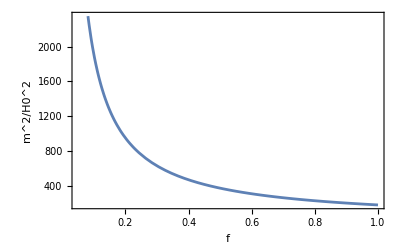

```mathematica
(*Regiones de f donde vamos a tener una masa positiva si β=H0^4*)
m[H0,H0^4,f]//Simplify
Reduce[(m[H0,H0^4,f])>=0&&H0>0,f,Reals]//N
Plot[((m[H0,H0^4,f])/H0^2//Simplify),{f,0,1},Frame->True,FrameLabel->{"f","m^2/H0^2"},PlotRange->{{0.05,1},Automatic}]
```

```mathematica
(*Ahora si, a resolver la Ec. de Klein Gordon □h-mh=0 h''(t)+3H0​h'(t)+(Exp[-2H0​t]k^2​+m^2)h(t)=0, con h(t,z)=hk​(t)Exp[ikz]
y □h=g[μ,ν]Nabla[-μ]Nabla[-ν]h=1/Sqrt[-g] ∂[μ](Sqrt[-g]g[μ,ν]∂[-ν]h) *)
fValues={0.01,0.1,1,10};

H0val={67,74};
kval=1;

Sols=Table[mval=m[H0,H0^4,f]/. {H0->H0val[[j]],f->fval};
eqKG=h''[t]+3 H0val[[j]] h'[t]+(Exp[-2 H0val[[j]] t] kval^2+mval) h[t]==0;
NDSolveValue[{eqKG,h[0]==1,h'[0]==0},h,{t,0,5}],{fval,fValues},{j,1,2}];
```

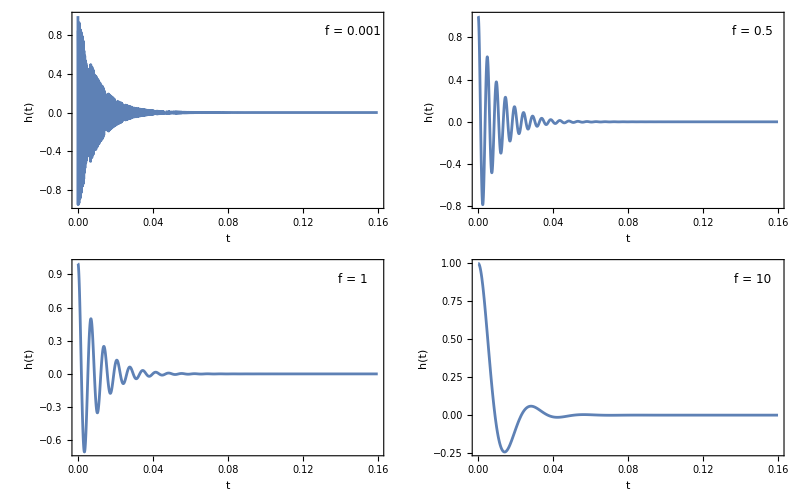

```mathematica
GraphicsGrid[Partition[Table[Plot[Evaluate[Sols[[i]]][t],{t,0,0.16},Frame->True,FrameLabel->{"t","h(t)"},PlotRange->All,Epilog->Inset[Style[Row[{"f = ",fValues[[i]]}],12],Scaled[{0.90,0.90}]]],{i,1,4}],2],Spacings->{0.5,0.5}]
```

```mathematica
m2δ=-Ro (2x^2-5x+1)/(3x(2x-3))
```

-(Ro (1-5 x+2 x^2))/(3 x (-3+2 x))

```mathematica
Rbar=12 H0^2;
(*ρΛ with β->1*)
rhoSol=(432 ⅇ^((f β)/(144 H0^4)) H0^6 k)/(144 H0^4-f)/.β->1//Simplify;
MassPaper=-Rbar (2 x^2-5 x+1)/(3 x (2 x-3));
MassPaperSub=MassPaper/. x->f/Rbar^2//Simplify;
MasaMine=(-κ+2 ρ f2'[Rbar]-2 Rbar ρ f2''[Rbar])/(6 ρ f2''[Rbar])/. {f2->Function[R,Exp[-f/R^2]],ρ->rhoSol}/.κ->k//FullSimplify;
Print["Masa δR:", MassPaperSub]
Print["Masa obtenida por g->g+h:", MasaMine]
Print["Diferencia:",MassPaperSub-MasaMine]
```

Masa δR obtenida por la Ruta Javier:-(4 H0^2 (f^2-360 f H0^4+10368 H0^8))/(f (f-216 H0^4))

Masa obtenida por g->g+h:-(4 H0^2 (f^2-360 f H0^4+10368 H0^8))/(f (f-216 H0^4))

Diferencia:0

#### scalaron in z-terms

```mathematica
(*where q and m are adimensional, divided by H0*)
heqz=(1+z)^2 h''[z]-2 (1+z) h'[z]+((q^2(1+z)^2+m^2)) h[z]==0;
(*Initial conditions*)
Cond={h[0]==1,h'[0]==0};
hSol=DSolve[{heqz,h[0]==1,h'[0]==0},h[z],z];
hSolz[qval_,mval_,zval_]:=hSol[[1,1,2]]/. {q->qval,m->mval,z->zval};
mvals=-((4 (10368-360 f+f^2))/((-216+f) f))/. f->{1/100,1/10,1,10};
hSolz[q,m,z]//FullSimplify
```

1/4 π (1+z)^(3/2) ((-((3+√(9-4 m^2)) BesselJ[1/2 √(9-4 m^2),q])+2 q BesselJ[1/2 (2+√(9-4 m^2)),q]) BesselY[1/2 √(9-4 m^2),q+q z]+BesselJ[1/2 √(9-4 m^2),q+q z] ((3+√(9-4 m^2)) BesselY[1/2 √(9-4 m^2),q]-2 q BesselY[1/2 (2+√(9-4 m^2)),q]))

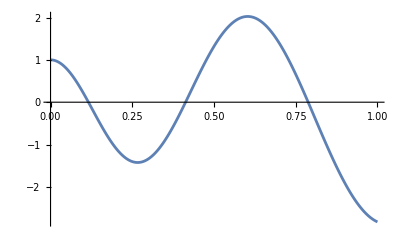

```mathematica
Plot[Evaluate[hSolz[1,mvals[[4]],z]],{z,0,1},WorkingPrecision->100,PlotPoints->1000,MaxRecursion->5]
```

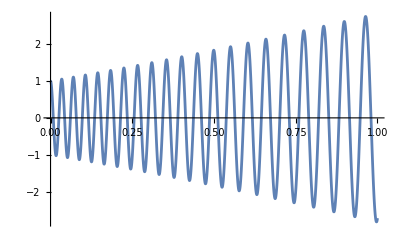

```mathematica
sol1=NDSolveValue[{heqz/. {q->1,m->mvals[[3]]},Cond},h,{z,0,1}];
Plot[sol1[z],{z,0,1}]
```

#### Envelope Function

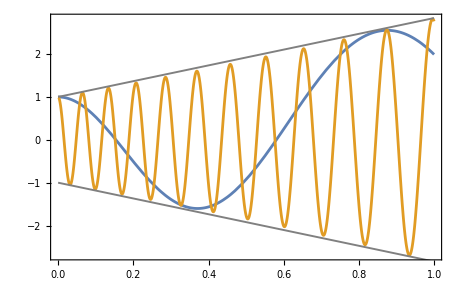

```mathematica
envZ[z_]:=1+1.84z (*Supoiendo algun ajuste lineal en la envolvente*)
sol1=NDSolveValue[{heqz/. {q->1,m->10},Cond},h,{z,0,1}];
sol2=NDSolveValue[{heqz/. {q->1,m->100},Cond},h,{z,0,1}];
pltSols=Plot[{sol1[z],sol2[z]},{z,0,1}];
pltEnv=Plot[{envZ[z],-envZ[z]},{z,0,1},PlotStyle->{Directive[Gray,Thickness[0.003]],Directive[Gray,Thickness[0.003]]}];
Show[{pltSols,pltEnv},Frame->True]
```